```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/Desktop/dataset.csv,/Users/yaroslav/Desktop/datasethi.csv,/Users/yaroslav/Desktop/hi.csv,/Users/yaroslav/Desktop/Untitled.csv}

```mathematica
importfile = files⟦1⟧
```

```mathematica
raw={{"V", "R"}, {0, 238}, {0.39, 110}, {0.67, 70}, {0.82, 50}, {1.26, 34}, {1.44, 26}, {1.64, 16}, {1.85, 15}, {2.05, 14}, {2.26, 10}}
```

{{V,R},{0,238},{0.39,110},{0.67,70},{0.82,50},{1.26,34},{1.44,26},{1.64,16},{1.85,15},{2.05,14},{2.26,10}}

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

{{a,n},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}

```mathematica
dataset=makeDataset[raw]
```

```mathematica
datasetWE=dataset[All,<|"V"->(Around[#V,0.01]&),"R"->(10Around[#R,1]&)|>]
```

```mathematica
datasetWE//Normal
```

```mathematica
datasetWE=Dataset[{<|"V"->0,"R"->2380.10.|>,<|"V"->0.3900.010,"R"->1100.10.|>,<|"V"->0.6700.010,"R"->700.10.|>,<|"V"->0.8200.010,"R"->500.10.|>,<|"V"->1.2600.010,"R"->340.10.|>,<|"V"->1.4400.010,"R"->260.10.|>,<|"V"->1.6400.010,"R"->160.10.|>,<|"V"->1.8500.010,"R"->150.10.|>,<|"V"->2.0500.010,"R"->140.10.|>,<|"V"->2.2600.010,"R"->100.10.|>}]
```

```mathematica
dataset1=datasetWE[All,<|"V"->(#V&),"T"->(273.16+Around[25,1]+(10^3#V)/Around[41,1]&),"R"->(#R&)|>]
```

```mathematica
dataset2=dataset1[All,<|"V"->(#V&),"R"->(#R&),"Tinv"->(10^3(#T)^-1&),"lnR"->(Log[(#R)/Around[2380,10]]&)|>]
```

```mathematica
dataset2//Normal
```

```mathematica
dataset2=Dataset[{<|"V"->0,"R"->2380.10.,"Tinv"->3.3540.011,"lnR"->0|>,<|"V"->0.3900.010,"R"->1100.10.,"Tinv"->3.2500.011,"lnR"->-0.7720.010|>,<|"V"->0.6700.010,"R"->700.10.,"Tinv"->3.1800.011,"lnR"->-1.2240.015|>,<|"V"->0.8200.010,"R"->500.10.,"Tinv"->3.1430.011,"lnR"->-1.5600.020|>,<|"V"->1.2600.010,"R"->340.10.,"Tinv"->3.0410.012,"lnR"->-1.9460.030|>,<|"V"->1.4400.010,"R"->260.10.,"Tinv"->3.0000.012,"lnR"->-2.210.04|>,<|"V"->1.6400.010,"R"->160.10.,"Tinv"->2.9570.012,"lnR"->-2.700.06|>,<|"V"->1.8500.010,"R"->150.10.,"Tinv"->2.9130.013,"lnR"->-2.760.07|>,<|"V"->2.0500.010,"R"->140.10.,"Tinv"->2.8720.013,"lnR"->-2.830.07|>,<|"V"->2.2600.010,"R"->100.10.,"Tinv"->2.8310.014,"lnR"->-3.170.10|>}]
```

```mathematica
dataset2=Dataset[{<|"V"->0,"R"->2380.10.,"Tinv"->3.3540.012,"lnR"->0|>,<|"V"->0.3900.010,"R"->1100.10.,"Tinv"->3.2500.011,"lnR"->-0.7720.010|>,<|"V"->0.6700.010,"R"->700.10.,"Tinv"->3.1800.011,"lnR"->-1.2240.015|>,<|"V"->0.8200.010,"R"->500.10.,"Tinv"->3.1430.011,"lnR"->-1.5600.020|>,<|"V"->1.2600.010,"R"->340.10.,"Tinv"->3.0410.012,"lnR"->-1.9460.030|>,<|"V"->1.4400.010,"R"->260.10.,"Tinv"->3.0000.012,"lnR"->-2.210.04|>,<|"V"->1.6400.010,"R"->160.10.,"Tinv"->2.9570.012,"lnR"->-2.700.06|>,<|"V"->1.8500.010,"R"->150.10.,"Tinv"->2.9130.013,"lnR"->-2.760.07|>,<|"V"->2.0500.010,"R"->140.10.,"Tinv"->2.8720.013,"lnR"->-2.830.07|>,<|"V"->2.2600.010,"R"->100.10.,"Tinv"->2.8310.014,"lnR"->-3.170.10|>}]
```

```mathematica
dataset3=dataset2[All,<|"V"->(hiTeXForm[#V]&),"R"->(hiTeXForm[#R]&),"Tinv"->(hiTeXForm[#Tinv]&),"lnR"->(hiTeXForm[#lnR]&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"data.csv",dataset3,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.3/data.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

FittedModel[-19.9232+5.89535 x]

-19.90.8

5.900.25

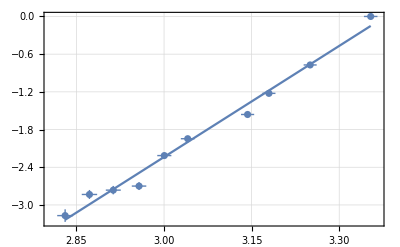

```mathematica
data={{3.353903944191038,0},{3.250212452911556,-0.7717903078790584},{3.1796354431636287,-1.2237754316221157},{3.14307266784008,-1.5602476682433286},{3.040514484714369,-1.9459101490553132},{3.0004625103186635,-2.2141741356499924},{2.9571800331204163,-2.6996819514316934},{2.9130573175999817,-2.7642204725692645},{2.8722426470588234,-2.833213344056216},{2.8306003081902382,-3.169685580677429}};
dataerr=Table[{dataset2[n,"Tinv"],dataset2[n,"lnR"]},{n,10}];
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr,Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"10^{-3} \\cdot T^{-1},\\text{ K}^{-1}","\\ln \\left(R /R_0 \\right)"}],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

```mathematica
Table[{dataset2[n,"Tinv"]["Value"],dataset2[n,"lnR"]["Value"]},{n,10}]
```

```mathematica
{{3.353903944191038,0},{3.250212452911556,-0.7717903078790584},{3.1796354431636287,-1.2237754316221157},{3.14307266784008,-1.5602476682433286},{3.040514484714369,-1.9459101490553132},{3.0004625103186635,-2.2141741356499924},{2.9571800331204163,-2.6996819514316934},{2.9130573175999817,-2.7642204725692645},{2.8722426470588234,-2.833213344056216},{2.8306003081902382,-3.169685580677429}}
```

```mathematica
{{3353.903944191038,0},{3250.2124529115563,-0.7717903078790584},{3179.6354431636287,-1.2237754316221157},{3143.07266784008,-1.5602476682433286},{3040.5144847143692,-1.9459101490553132},{3000.4625103186636,-2.2141741356499924},{2957.1800331204163,-2.6996819514316934},{2913.0573175999816,-2.7642204725692645},{2872.2426470588234,-2.833213344056216},{2830.600308190238,-3.169685580677429}}
```

```mathematica
5.900.25 1000 1.38 10^-23/1.6 10^19
```

0.5080.021